```mathematica
附录A
```

```mathematica
Δ=x (s/2-x);equ=D[Δ,x]==0;Solve[equ,x]
```

{{x→s/4}}

```mathematica
equ={x+y==s/2,Δ==x y};Solve[equ,Δ,y]
```

{{Δ→-1/2 x (-s+2 x)}}

```mathematica
equ1=x+y==s/2;equ2=Δ==x y;
Δ=Δ/.First[Solve[{equ1,equ2},Δ,y]];
equ=D[Δ,x]==0;
x=x/.First[Solve[equ,x]];Print["x = ",x];
y=y/.First[Solve[equ1,y]];Print["y = ",y]
```

x = s/4

y = s/4

{25/4,{x→5/2}}

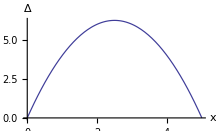

```mathematica
s=10;Δ=x (s/2-x);Maximize[Δ,x]
Plot[Δ,{x,0,s/2},AxesLabel->{"x","Δ"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
```

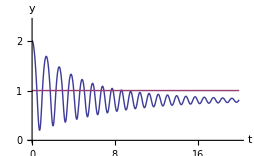

```mathematica
g=9.8;k=50;L=1;h=2;α=0.3;time=20;
equ={y''[t]==-α y'[t]-g+If[y[t]≥L,0,
k (L-y[t])],y[0]==h,y'[0]==0};
s=NDSolve[equ,y,{t,0,time}];
Plot[{y[t]/.s,L},{t,0,time},
PlotRange->{0,1.2h},AxesLabel->{"t","y"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[g,k,L,h,equ,s,α,time]
```